# Enumerative Combinatorics - Introduction

We are going to explore the combinatorial structures provided in the first lecture using Mathematica.

## Words

We will explore the definition of a word over a finite alphabet in this section and explore the theorems using the combinatorics package of Mathematica.

Recall that given a finite set A, which we called alphabet, a word is a finite sequence of elements of A. The first theorem is as follows.

Theorem 1.1: The number of words of length k in an alphabet consisting of n letters is equal to n^k.

First, we create a finite set containing integers and then we will calculate the number of words of length k.

```mathematica
A=Range[1,4]
```

{1,2,3,4}

Now, let us evaluate all possible words of length 2 over the alphabet A.

```mathematica
Tuples[A, 2]
```

{{1,1},{1,2},{1,3},{1,4},{2,1},{2,2},{2,3},{2,4},{3,1},{3,2},{3,3},{3,4},{4,1},{4,2},{4,3},{4,4}}

Let us do the same but with words of length 3.

```mathematica
Tuples[A, 3]
```

{{1,1,1},{1,1,2},{1,1,3},{1,1,4},{1,2,1},{1,2,2},{1,2,3},{1,2,4},{1,3,1},{1,3,2},{1,3,3},{1,3,4},{1,4,1},{1,4,2},{1,4,3},{1,4,4},{2,1,1},{2,1,2},{2,1,3},{2,1,4},{2,2,1},{2,2,2},{2,2,3},{2,2,4},{2,3,1},{2,3,2},{2,3,3},{2,3,4},{2,4,1},{2,4,2},{2,4,3},{2,4,4},{3,1,1},{3,1,2},{3,1,3},{3,1,4},{3,2,1},{3,2,2},{3,2,3},{3,2,4},{3,3,1},{3,3,2},{3,3,3},{3,3,4},{3,4,1},{3,4,2},{3,4,3},{3,4,4},{4,1,1},{4,1,2},{4,1,3},{4,1,4},{4,2,1},{4,2,2},{4,2,3},{4,2,4},{4,3,1},{4,3,2},{4,3,3},{4,3,4},{4,4,1},{4,4,2},{4,4,3},{4,4,4}}

Let us calculate all words up to length 15 and plot the result.

```mathematica
data=Table[{n, Length[Tuples[A,n]]},{n,8}]
```

{{1,4},{2,16},{3,64},{4,256},{5,1024},{6,4096},{7,16384},{8,65536}}

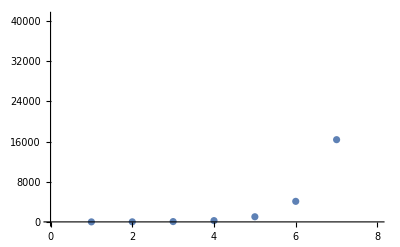

```mathematica
ListPlot[data]
```

Since we are dealing with an exponential function,  it growth rapidly . However, the above is kind of an experimental verification of Theorem 1.1.

The second definition of the lecture deals with the number of permutations. Recall that a permutation is a bijection from {1, 2,..., n} to itself. The number of such permutations is provided by the following theorem.

Theorem 1.2: The number of permutations of {1,2,...,n} is equal to n! = 1 ·2···n.

Let us test the above theorem using Mathematica.

```mathematica
Permutations[Range[1,4]]
```

{{1,2,3,4},{1,2,4,3},{1,3,2,4},{1,3,4,2},{1,4,2,3},{1,4,3,2},{2,1,3,4},{2,1,4,3},{2,3,1,4},{2,3,4,1},{2,4,1,3},{2,4,3,1},{3,1,2,4},{3,1,4,2},{3,2,1,4},{3,2,4,1},{3,4,1,2},{3,4,2,1},{4,1,2,3},{4,1,3,2},{4,2,1,3},{4,2,3,1},{4,3,1,2},{4,3,2,1}}

```mathematica
Length[Out[27]]
```

24

```mathematica
4!
```

24

Recall that a k-permutation is a total linear ordering on a k-subset of {1,2,...,n}. The number of k-permutations has been proven in the lecture by the following theorem.

Theorem 1.3: The number of k-permutations of {1,2,...,n} is equal to n(n-1)···(n-k+1).

Generating all k-permutations is fairly simple in Mathematica. Consider the following code.

```mathematica
Permutations[Range[1,4],{2}]
```

{{1,2},{1,3},{1,4},{2,1},{2,3},{2,4},{3,1},{3,2},{3,4},{4,1},{4,2},{4,3}}

```mathematica
Permutations[Range[1,4],{3}]
```

{{1,2,3},{1,2,4},{1,3,2},{1,3,4},{1,4,2},{1,4,3},{2,1,3},{2,1,4},{2,3,1},{2,3,4},{2,4,1},{2,4,3},{3,1,2},{3,1,4},{3,2,1},{3,2,4},{3,4,1},{3,4,2},{4,1,2},{4,1,3},{4,2,1},{4,2,3},{4,3,1},{4,3,2}}

```mathematica
Permutations[Range[1,4], {1}]
```

{{1},{2},{3},{4}}

```mathematica
Permutations[Range[1,4],{0}]
```

{{}}

```mathematica
Length[Permutations[Range[1,3], {2}]]
```

6

```mathematica
3*(3-2+1)
```

6

The binomial coefficients describe the number of k-element subsets of a set {1,2,...,n} (“n choose k”).
Theorem 1.5: The number of k-element subsets of a set with cardinality n is equal to .

Calculating the binomial coefficients is easy . Consider the following code.

```mathematica
Binomial[10,2]
```

45

We can also generate the Pascal triangle as follows.

```mathematica
Column[Table[Binomial[n,k],{n,0,6},{k,0,n}], Center]
```

{1}
{1,1}
{1,2,1}
{1,3,3,1}
{1,4,6,4,1}
{1,5,10,10,5,1}
{1,6,15,20,15,6,1}